ODEs. Integrating Factors. Test for exactness. If exact, solve. If not, use an integrating factor as given or obtained by inspection or by the theorems in the text. Also, if an initial condition is given, find the corresponding particular solution.

1. 2xy dx + x^2 dy = 0

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn = 2 x y[x]+x^2 y'[x]==0;
sol = DSolve[eqn,y,x]
```

{{y→Function[{x},C[1]/x^2]}}

```mathematica
eqn/.sol
```

{True}

```mathematica
ClearAll["Global`*"]
```

2. x^3+y[x]^3 y'[x]=0

```mathematica
eqn=x^3+y[x]^3 y'[x]==0;
sol = DSolve[eqn,y,x]
```

{{y→Function[{x},-(-x^4+4 C[1])^(1/4)]},{y→Function[{x},-ⅈ (-x^4+4 C[1])^(1/4)]},{y→Function[{x},ⅈ (-x^4+4 C[1])^(1/4)]},{y→Function[{x},(-x^4+4 C[1])^(1/4)]}}

```mathematica
eqn/.sol[[1]]
```

True

```mathematica
eqn/.sol[[2]]
```

True

```mathematica
eqn/.sol[[3]]
```

True

```mathematica
eqn/.sol[[4]]
```

True

3. sin x cos y + cos x sin yy' = 0

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn = Sin[x] Cos[y[x]]+Cos[x] Sin[y[x]] y'[x]==0;
sol = DSolve[eqn, y, x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},-ArcCos[1/2 C[1] Sec[x]]]},{y→Function[{x},ArcCos[1/2 C[1] Sec[x]]]}}

```mathematica
eqn/.sol[[1]]
```

True

```mathematica
eqn/.sol[[2]]
```

True

4. ⅇ^(3 θ)(r'[θ]+3 r[θ])=0

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn=ⅇ^(3 θ)(r'[θ]+3 r[θ])==0;
sol = DSolve[eqn,r,θ]
```

{{r→Function[{θ},ⅇ^(-3 θ) C[1]]}}

```mathematica
eqn/.sol
```

{True}

5. (x^2+y^2)-2xyy'=0

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn=x^2+y[x]^2-2 x y[x] y'[x]==0;
sol = DSolve[eqn,y,x]
```

{{y→Function[{x},-√x √(x+C[1])]},{y→Function[{x},√x √(x+C[1])]}}

```mathematica
Simplify[eqn/.sol[[1]]]
```

True

```mathematica
Simplify[eqn/.sol[[2]]]
```

True

6. 3(y+1)=2xy', (y+1)x^-4

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn=3 (y[x]+1)==2 x y'[x];
sol = DSolve[eqn,y,x]
```

{{y→Function[{x},-1+x^(3/2) C[1]]}}

```mathematica
eqn/.sol
```

{True}

7. 2x tan y + sec^2 y y' = 0

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn = 2 x Tan[y[x]]+Sec[y[x]]^2 y'[x]==0;
sol = DSolve[eqn,y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},ArcCot[ⅇ^(x^2-2 C[1])]]}}

```mathematica
Simplify[eqn/.sol]
```

{True}

8. ⅇ^x(cos y -sin y y') = 0

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn = ⅇ^x (Cos[y[x]]-Sin[y[x]] y'[x])==0;
sol = DSolve[eqn,y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},-ArcCos[ⅇ^(-x-C[1])]]},{y→Function[{x},ArcCos[ⅇ^(-x-C[1])]]}}

```mathematica
Simplify[eqn/.sol[[1]]]
```

True

```mathematica
Simplify[eqn/.sol[[2]]]
```

True

9. ⅇ^(2x)(2 cos y - sin y y')=0, y(0)=0

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn = ⅇ^(2 x) (2 Cos[y[x]]-Sin[y[x]] y'[x])==0;
sol = DSolve[{eqn,y[0]==0},y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

{{y→Function[{x},-ArcCos[ⅇ^(-2 x)]]},{y→Function[{x},ArcCos[ⅇ^(-2 x)]]}}

```mathematica
Simplify[eqn/.sol[[1]]]
```

True

```mathematica
Simplify[eqn/.sol[[2]]]
```

True

10. y+(y + tan(x+y))y' = 0, cos(x + y) [or 2(cos x cos y)]

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn=y[x] +(y[x]+Tan[x+y[x]]) y'[x] ==0;
```

```mathematica
sol = DSolve[eqn,y,x]//Simplify
```

Solve[C[1]==Sin[x+y[x]] y[x],y[x]]

WolframAlpha comes up with the same thing. I don’t know how to untangle it. I don’t think the following plot is correct, but I stick it in anyway.

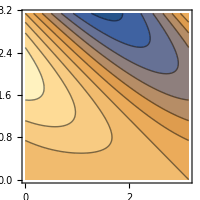

```mathematica
ContourPlot[Sin[x+y] y,{x,0,π},{y,0,π},ImageSize->200]
```

11. 2cosh x cos y = sinh x siny y'

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn = 2 Cosh[x] Cos[y[x]]==Sinh[x] Sin[y[x]]y'[x];
sol = DSolve[eqn,y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},-ArcCos[-1/2 ⅈ C[1] Csch[x]^2]]},{y→Function[{x},ArcCos[-1/2 ⅈ C[1] Csch[x]^2]]}}

```mathematica
Simplify[eqn/.sol[[1]]]
```

True

```mathematica
Simplify[eqn/.sol[[2]]]
```

True

12. (2xy + y') ⅇ^(x^2) = 0, y(0) = 2

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn = (2 x y[x]+y'[x]) ⅇ^(x^2)==0;
sol = DSolve[{eqn,y[0]==2},y,x]
```

{{y→Function[{x},2 ⅇ^(-x^2)]}}

```mathematica
eqn/.sol
```

{True}

13. ⅇ^(-y[x]) + ⅇ^-x (-ⅇ^(-y[x])+1) y'[x] = 0, F = ⅇ^(x+y[x])

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn = ⅇ^(-y[x])+ⅇ^-x (-ⅇ^(-y[x])+1) y'[x]==0;
sol = DSolve[eqn,y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},ⅇ^x-C[1]-ProductLog[-ⅇ^(ⅇ^x-C[1])]]}}

```mathematica
Simplify[eqn/.sol]
```

{True}

14. (a+1) y + (b+1) x y' = 0, y(1) = 1, F = x^a y^b

```mathematica
ClearAll["Global`*"]
```

```mathematica
eqn = (a+1) y[x]+(b+1) x y'[x]==0;
sol = DSolve[{eqn,y[1]==1},y,x]
```

{{y→Function[{x},(1+b)^(1/(1+b)+a/(1+b)) (x+b x)^(-1/(1+b)-a/(1+b))]}}

```mathematica
Simplify[eqn/.sol]
```

{True}

15.  Exactness. Under what conditions for the constants a, b, k, l is (a x + b y)dx + (k x + l y)dy = 0 exact? Solve the exact ODE.

```mathematica
ClearAll["Global`*"]
```

According to the exactness test, b = k. The text answer also has the relationship a*x^2 + 2*k*x*y + l*y^2 = c, but I haven’t been able to track this down yet. As for the exact equation, (and substituting b for k)

```mathematica
eqn = y'[x]==-(a x + b y[x])/(b x + l y[x])
```

y'[x]==-(a x+b y[x])/(b x+l y[x])

```mathematica
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},(-b x-√(ⅇ^(2 C[1]) l+b^2 x^2-a l x^2))/l]},{y→Function[{x},(-b x+√(ⅇ^(2 C[1]) l+b^2 x^2-a l x^2))/l]}}

```mathematica
FullSimplify[eqn/.sol[[1]]]
```

True

```mathematica
FullSimplify[eqn/.sol[[2]]]
```

True